Поле для ввода

Поле расчета

# Уравнение Хопфа:

```mathematica
Subscript[u, 0][x_]:=-x/(1+x^2)
```

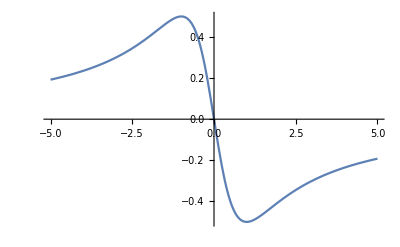

```mathematica
Plot[Subscript[u, 0][t],{t,-5,5}]
```

```mathematica
x[u]:=Solve[{u==Subscript[u, 0][x]},{x},Reals][[1]][[1]]
```

```mathematica
res = x[u]
```

x→ConditionalExpression[-1/(2 u)-1/2 √((1-4 u^2)/u^2), -1/2<u<1/2]

```mathematica
Subscript[x, 0]=x/.res
```

ConditionalExpression[-1/(2 u)-1/2 √((1-4 u^2)/u^2), -1/2<u<1/2]

```mathematica
x[t_]:=u*t+Subscript[x, 0]
```

```mathematica
x[t]
```

ConditionalExpression[-1/(2 u)+t u-1/2 √((1-4 u^2)/u^2), -1/2<u<1/2]

## Решение из конспекта:

```mathematica
Subscript[u, 0][x_]:= ArcCot[x]
```

```mathematica
ans = Solve[D[Subscript[u, 0][x], {x, 2}] == 0][[1]]
```

{x→0}

```mathematica
Subscript[y, 0] =x/. ans;
```

```mathematica
free = SeriesCoefficient[Subscript[u, 0][x], {x, Subscript[y, 0], 0}]
```

π/2

```mathematica
Subscript[c, 1] = -SeriesCoefficient[Subscript[u, 0][x], {x, Subscript[y, 0], 1}]
```

1

```mathematica
Subscript[c, 2] = SeriesCoefficient[Subscript[u, 0][x], {x, Subscript[y, 0], 3}]
```

1/3

```mathematica
Subscript[t, шок] =1/Subscript[c, 1]
```

1

```mathematica
Answer = free -(Subscript[c, 1]^4/Subscript[c, 2](x - (Subscript[y, 0] + free/Subscript[c, 1])))^(1/3)
```

```mathematica
ы
```

π/2-3^(1/3) (-π/2+x)^(1/3)

# Возмущение осциллятора:

```mathematica
G[x_, y_]:= (β + x^2 - x^4)y
```

```mathematica
da = ϵ/(2π)Integrate[Sin[ϕ] G[a Cos[ϕ], a Sin[ϕ]], {ϕ, 0, 2π}]
```

-1/16 a (-2 a^2+a^4-8 β) ϵ

```mathematica
dτ = ϵ/(2π)Integrate[Cos[ϕ]/a G[a Cos[ϕ], a Sin[ϕ]], {ϕ, 0, 2π}]
```

0

# Возмущение осциллятора, зависящее от времени:

```mathematica
G[x_, y_,t_]:= x*Cos[2*t]
```

```mathematica
da = ϵ/(2π)Integrate[Sin[τ-t+ϕ] G[a Cos[τ-t+ϕ], a Sin[τ-t+ϕ],t-ϕ], {ϕ, 0, 2π}]
```

1/2 a ϵ Cos[τ] Sin[τ]

```mathematica
dτ = ϵ/(2π)Integrate[Cos[τ-t+ϕ]/a G[a Cos[τ-t+ϕ], a Sin[τ-t+ϕ],t-ϕ], {ϕ, 0, 2π}]
```

1/4 ϵ Cos[2 τ]

# Уравнение Бюргерса:

Errfc = 1 - Errf, Errfi = -i Errf(iz)

```mathematica
Subscript[u, 0][x_]:= Piecewise[{{a, x>0}, {0, x<0}}]
```

```mathematica
Subscript[ϕ, 0][y_] := Exp[-1/2 Integrate[Subscript[u, 0][z], {z ,0, y}]]
```

```mathematica
ψ[t_, x_]:= 1/(√(4 π t))Assuming[y∈Reals && t > 0 && t∈Reals,Integrate[Exp[-(x-y)^2/(4t)] * Subscript[ϕ, 0][y],{y, -∞, +∞}]]
```

```mathematica
psi = ψ[t, x]
```

1/2 (ⅇ^(1/4 a (a t-2 x))+ⅇ^(1/4 a (a t-2 x)) Erf[(-a t+x)/(2 √t)]+Erfc[x/(2 √t)])

```mathematica
u = Simplify[-2 * D[Log[psi], x]]
```

(a (1+Erf[(-a t+x)/(2 √t)]))/(1+Erf[(-a t+x)/(2 √t)]+ⅇ^(-1/4 a (a t-2 x)) Erfc[x/(2 √t)])

# Огибающая волнового пакета

```mathematica
G[u_,dxu_,dtu_]:=-dtu*dxu^2
```

```mathematica
res =FullSimplify[ (ⅈ*ϵ)/ω*Exp[ⅈ*θ]*Integrate[Exp[-ⅈ*ϕ]/(2π)*G[a*Cos[ϕ],-q*a*Sin[ϕ],ω*a*Sin[ϕ]],{ϕ,0,2π}]]
```

-3/8 a^3 ⅇ^(ⅈ θ) q^2 ϵ

Also note that ψ = a * exp (i*θ) and get result